```mathematica
SetDirectory[NotebookDirectory[]];

tA[]:=(CasZ=SessionTime[];DateZ=DateString[{ "Start ","Time", " ","DayName", " ","Day", "/","Month"}];Date1=Date[];);
tB[]:=(CasK=SessionTime[];DateK=DateString[{ "Konec ","Time", " ","DayName", " ","Day", "/","Month"}];Date2=Date[];
Print[DateString[Date2-Date1,{ "TIME"," ","Time"," ","Day"}]<>"  #  "<>DateZ<>" / "<>DateK];);
```

# Definice jednotlivych funkci pro detekci signal vs. chaos

## 1. Box-counting method

```mathematica
BoxCount[list_,delta0_,scale_,min_]:=  (*Pôvodný algoritmus na určenie množiny dvojíc (epsilon, pocet potrebnych stvorcov na pokrytie množiny)*)
Block[{tmp,delta,nmax,l,i},tmp={};

delta=delta0;
nmax=Abs[Ceiling[Log[min/delta0]/Log[scale]]];

Do[
{
l=Length[Complement[Ceiling[list/delta],tmp]];
AppendTo[tmp,{delta,l}];
delta=delta* scale
},
{i,1,nmax}];

Return[tmp]];  
odhadDimenze[{x_,y_}]:=N[{-Log[10,x],Log[10,y]}]; (*Logaritmuje predchadzajuci vystup, ktory po Fite LSM určí odhad frakt. dimenzie*)

BoxCount1[dataa_]:=((*Zautomatizuje predchádzajúce algoritmy, pre vstupnú množinu dát udá frakt. dimenziu, je oštrený prípad keď bude po fite hodnota iba skalár*)
Clear[x,EHM,EHM0,EHM1,EHM2,EHM3,n2,n1];

EHM =BoxCount[(dataa/Max[dataa])+0.,1.0,0.5,0.001];
EHM1=Map[odhadDimenze,EHM];
EHM1;
EHM2 = Fit[Take[EHM1,Take[Length[EHM1]]],{1,x},x];
EHM2;
If[Length[EHM2]<1,0,
EHM3 = Take[EHM2,-1]/x;
EHM3 ]
);
```

```mathematica
(*BoxCount1[dataa_]:=((*Zautomatizuje predchádzajúce algoritmy, pre vstupnú množinu dát udá frakt. dimenziu, je oštrený prípad keď bude po fite hodnota iba skalár*)
Clear[x,EHM,EHM5,EHM1,EHM2,EHM3,n,n1];
Module[{n,EHM1,EHM2,EHM3,EHM4,EHM5},
dataaa=  EMB3[dataa];
EHM =BoxCount[dataaa,1.0,0.5,0.0000000000001];

EHM1=Map[odhadDimenze,EHM];
EHM1;
n=1;
While[EHM1[[n]][[2]]  ≠  EHM1[[n+1]][[2]],n ;n++];
EHM5= Take[EHM1,n-1];
EHM2 = Fit[Take[EHM5,Take[Length[EHM5]]],{1,x},x];
EHM2;
If[Length[EHM2]<1,0,
EHM3 = Take[EHM2,-1]/x;
EHM3 ]]
);*)
```

## 2. Korelačná dimenzia -D2

```mathematica
corrDIMdim[DData_] := ((*Pocita korelacnu dimenziu pre nejake vstupne data , je osetreny pripad ked je po Fite skalar*)
Clear[my,x,CDIM,fit,r,nF,i];
my=Log[10,N[Module[{nF=Nearest[DData->Automatic]},Table[{r,Tr[Table[Tr[UnitStep[nF[DData[[i]],{All,r}]-i-1]],{i,1,Length[DData]}]]},{r,0.001,0.011,0.001}]]]];
fit=Fit[my,{1,x},x];

If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]

);
```

```mathematica
er[dat_]:=  
(ST =StandardDeviation[dat];
cor[min_,max_,fac_]:=  
min*( fac ^Range[Floor[Log[ max/ min] / Log[fac]]]);
cor[0.1*ST,0.5*ST,1.03])

 (*data={Drop[dataa,-1],Drop[dataa,1]}ᵀ;
data={Drop[dataa,-2],Take[dataa,{2,-2}],Drop[dataa,2]}ᵀ;*)

EMB1[dataa_]:=(
data={Drop[dataa,-1],Drop[dataa,1]}ᵀ
);


EMB3[data_]:={Drop[data,-2],Take[data,{2,-2}],Drop[data,2]}ᵀ;





 (* corrDIMdim1[dataa_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=ParallelTable[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[ParallelTable[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];
fit = Fit[Flatten[Log[correlationSum[dataa,1,1,1,-3,0.1,11]],1],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]
);*)
```

```mathematica
corrDIMdim1[dataa_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[Table[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];
fit = Fit[Flatten[Log[correlationSum[dataa,1,1,1,-3,0.1,11]],1],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]);
```

```mathematica
(* corrDIMdim1[dataa_,em_,dtim_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[Table[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];
fit = Fit[DeleteCases[Log10[correlationSum[dataa,dtim,em,1,-3,0.1,11][[em]]],{_,Indeterminate}],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]
);*)
```

```mathematica
falseNearestNeighbors[data_,τ_,mMax_,T1_,T2_]:=Module[{emb,m,n,σ,count,nf,x,yPos,y,Rm,incr},
emb=Table[Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}],{m,mMax+1}];
n=Length/@emb;
σ=StandardDeviation[data];
Table[count=0;
nf=Nearest[emb⟦m⟧->Range[n⟦m⟧]];
Do[x=emb⟦m,i⟧;
yPos=Last[nf[x,2]];
If[yPos≤n⟦m⟧-τ,y=emb⟦m,yPos⟧,Continue[]];
Rm=EuclideanDistance[x,y];
incr=Abs[Last[emb⟦m+1,i⟧]-Last[emb⟦m+1,yPos⟧]];
Quiet@If[incr/Rm>T1||incr/σ>T2,count=count+1],{i,n⟦m+1⟧}];
{m,N[count/n⟦m+1⟧]},{m,mMax}]]


corrDIMdim1[dataa_]:=(
correlationSum[data_,τ_,mMax_,minΔt_Integer?(#≥1&),minExp_,maxExp_,nExp_]:=
Table[Module[{emb,nn,ed,bin,di},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
ed=Flatten[Table[di=emb⟦i⟧;
EuclideanDistance[di,#]&/@Take[emb,{i+minΔt,nn}],{i,nn-minΔt}]];
bin=N@Binomial[nn-minΔt+1,2];
{10.^#,Total[UnitStep[(10.^#)-ed]]/bin}&/@Range[minExp,maxExp,(maxExp-minExp)/(nExp-1)]],
{m,mMax}];

n=1;
While[falseNearestNeighbors[dataa,1,5,15,2][[n]][[2]]≠0 &&n<5,n;n++];
fit = Fit[DeleteCases[Log10[correlationSum[dataa,1,n,20,-3,0.5,18][[n]]],{_,Indeterminate}],{1,x},x];
If[Length[fit]==0,0,fit[[2]]/x]
);
```

```mathematica
(*averageMutualInformation[data_,τMax_,binWidth_]:=Module[{iter,n=Length[data],pi,pij},
ParallelTable[iter={Min[data],Max[data]+binWidth,binWidth};
pi=N[BinCounts[data,iter]/n];
pij=N[BinCounts[{Drop[data,-τ],Drop[data,τ]}ᵀ,iter,iter]/(n-τ)];
{τ,Total[DeleteCases[Flatten[pij Log2[pij/KroneckerProduct[pi,pi]]],Indeterminate|∞]]},{τ,0,τMax}]]*)

(*corrDIMdim1[data_]:=
(
dataa =  EMB3[data];
m=Table[{r,Total[Table[Length[Drop[Nearest[Drop[dataa,i-1],dataa[[i]],{All,r}],1]],{i,1,Length[dataa]}]]},{r,er[data]}];
fit=Fit[Log[10,m],{1,x},x];
If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]);*)
```

```mathematica
corrDIMdim1[data_]:=
(dataaa=  data/ Max[data];
dataa =  EMB3[dataaa];
(m=Table[{r,Total[Table[Length[Drop[Nearest[Drop[dataa,i-1],dataa[[i]],{All,r}],1]],{i,1,Length[dataa]}]]},{r,0.001,0.011,0.001}];
fit=Fit[Log[10,m],{1,x},x];

If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]));
```

```mathematica
corrDIMdim1[data_]:=
(dataaa= data/ Max[data];
dataa =  EMB3[dataaa];
(m=Table[{r,Total[Table[Length[Drop[Nearest[Drop[dataa,i-1],dataa[[i]],{All,r}],1]],{i,1,Length[dataa]}]]},{r,0.001,0.011,0.001}];

m=DeleteCases[m,{_,0}];

fit=Fit[Log[10,m],{1,x},x];

If[Length[fit]<1,0,
CDIM = Take[fit,-1]/x;
CDIM  ]));
```

## 3. Lyapunov exponent λ

```mathematica
Lyapun1[dataa_]:=( (*Lyapunov exonent, nastavený na parametre  Lya[dataa,1,1,0.001,20,1] tj. aby vytvoril z časovej rady iba 1 D priestor dĺžky 20 a zneho potom určil LCE. Berie do úvahy celý scaling region*)
Clear[x,EHM,EHM0,EHM1,EHM2,EHM3,n2,n1,DaTA];
Lya[data_,τ_,mMax_,ϵ_,δMax_,h_]:=
Table[Module[{emb,nn,nf,neigh},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
nf=Nearest[emb->Range[nn]];
neigh=Table[DeleteCases[Rest[nf[emb⟦t⟧,{∞,ϵ}]],p_/;p>nn-δMax],{t,nn-δMax}];
Table[{δ,Mean[DeleteCases[
Table[If[Length[neigh⟦t⟧]==0,"d",
Log[Mean[Abs[data⟦t+(m-1)τ+δ⟧-data⟦neigh⟦t⟧+(m-1)τ+δ⟧]]]],
{t,nn-δMax}],"d"|Indeterminate]]},
{δ,0,δMax}]],{m,mMax}];
s = Lya[dataa,1,1,0.001,20,1];
ll=Fit[s[[1]],{1,x},x][[2]]/x
);
```

```mathematica
Lyapun2[dataa_]:=(
Lya[data_,τ_,mMax_,ϵ_,δMax_,h_]:=
Table[Module[{emb,nn,nf,neigh},
emb=Table[Take[data,{i,i+τ(m-1),τ}],{i,Length[data]-τ(m-1)}];
nn=Length[emb];
nf=Nearest[emb->Range[nn]];
neigh=Table[DeleteCases[Rest[nf[emb⟦t⟧,{∞,ϵ}]],p_/;p>nn-δMax],{t,nn-δMax}];
SMT1 =Table[{δ,SMT2 =Mean[ SMT3=DeleteCases[
SMT4 =Table[If[Length[neigh⟦t⟧]==0,"d",
Log[Mean[Abs[data⟦t+(m-1)τ+δ⟧-data⟦neigh⟦t⟧+(m-1)τ+δ⟧]]]],
{t,nn-δMax}],"d"|Indeterminate]]},
{δ,0,δMax}]],{m,mMax}];
s = Lya[dataa,1,1,0.001,20,1];
ll=Fit[s[[1]],{1,x},x][[2]]/x;
If[Length[ll]>1,
n=1;While[
IntervalMemberQ[Interval[{-Infinity,Infinity}],SMT1[[n]][[2]]],Take[SMT1[[n]]];n++];
n;
If[n==1,0,lll=Fit[Take[s[[1]],n-1],{1,x},x][[2]]/x],ll]
 );
```

## 4. RQA

```mathematica
f1=Compile[{{n,_Real,1}},(Count[Flatten[UnitStep[0.1*Sqrt[Variance[n]]-Table[Sqrt[Abs[(n[[i]]-n[[j]])^2]],{i,1,Length[n]},{j,1,Length[n]}]]],1]-(Length[n]+1))/(Length[n]^2),CompilationTarget->"C",RuntimeAttributes->Listable,RuntimeOptions->"Speed"]


ClearAll[RpRR];
RpRR[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,DE},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
SR =Total[Total[R]];
RR=SR/(N1^2);
N[{RR}]
]

ClearAll[Rp1];
Rp1[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,DE},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
SR =Total[Total[R]];
RR=SR/(N1^2);
oneCount[list_,len_]:=Total@UnitStep[ListCorrelate[ArrayPad[ConstantArray[1,len],1,-1],list,{2,-2},0]-len];
DE =Total[Table[oneCount[Diagonal[R,i],1],{i,1,Length[Diagonal[R,1]]}]] ;
DET =(SR-2*DE )/SR;
N[{RR,DET}]
]

ClearAll[Rp3];
Rp3[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,ENTR,pp,F,L,l},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;

Smat[Mat_]:=(
oneCount[list_,len_]:=Total@UnitStep[ListCorrelate[ArrayPad[ConstantArray[1,len],1,-1],list,{2,-2},0]-len];
oo =Table[Table[oneCount[Diagonal[Mat,j],i],{i,1,Length[Diagonal[Mat,j]]}],{j,1,Length[Mat]-1}];
Yout =Total@Table[Flatten[{oo[[i]],Table[0,{i-1}]}],{i,Length[oo]}]
);
Yout=Smat[R];
S=2*Yout;
SR=0;
For[i=1,i<N1,i++,  
           SR=SR+i*S[[i]];];
RR=SR/(N1^2);
Lmin=2;
If[SR==0,
DET=0,
DET=(SR-Sum[S[[i]],{i,Lmin-1}])/SR;];

pp=S/Sum[S[[i]],{i,Length[S]}];
entropy=0;
F =Complement[Table[{i},{i,Lmin,Length[S]}],Position[S,0]];
l = Length[F];

If[l==0,ENTR=0,ENT = Table[pp[[F[[i]]]]*Log[pp[[F[[i]]]]],{i,1,Length[F]}];
ENTR = - Sum[ENT[[i]],{i,1,Length[ENT]}]
];
L =(SR-S[[1]])/Sum[S[[i]],{i,Lmin,Length[S]}];

N[{RR,DET,ENTR[[1]],L}]
]

ClearAll[RpAl];
RpAl[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j,L,ENTR},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
allSequences[list_]:=Tally[Length/@Split[list][[If[list[[1]]==1,1,2];;-1;;2]]];
dat=Flatten[Table[Flatten[{Diagonal[R,i],{0}}],{i,1,Length[R]-1}]];
TD =Total[Total[R]];
RR=TD/(N1^2);
oo =allSequences[dat];
s1 =SortBy[oo,#[[1]]&];
DET=(TD-2*s1 [[1]][[2]] )/TD;
L =(TD-2* s1[[1]][[2]])/Total[Table[s1[[i]][[2]]*2,{i,2,Length[s1]}]];
s2 =2* Table[s1[[i]][[2]],{i,1,Length[s1]}];
s3=Drop[s2,1] /Total[s2];
ENTR=-Total[Log[s3]*s3];
N[{RR,DET,ENTR,L}]
]

ClearAll[RpDiag];
RpDiag[data_]:=Module[{rr,N1,idx,R,SR,RR,DDE,DET,i,j},rr=0.01*Sqrt[Variance[data]];
N1=Length[data];
R=ConstantArray[0,{N1,N1}];
idx=Nearest[data->Automatic,data,{∞,rr}][[All,2;;]];
MapIndexed[{x,y}↦R[[y,x]]=1,idx];
R;
TOT[li_]:=Total[Select[kk,MemberQ[Take[#,1],li]&]][[2]];
ii =Table[allSequences[Diagonal[R,i]],{i,1,Length[R]-2}] ;
kk =SortBy[Flatten[Take[ii,Length[ii]],1],#[[1]]&] ;
po=Union[Table[kk[[i]][[1]],{i,1,Length[kk]}] ]; 
Yout =TOT/@po;
S=2*Yout;
TD =Total[Total[R]];
RR=TD/(N1^2);
DET=(TD-S[[1]])/TD;
L =(TD- S[[1]])/Total[Table[S[[i]],{i,2,Length[S]}]];
s3=Drop[S,1] /Total[S];
ENTR=-Total[Log[s3]*s3];
N[{RR,DET,ENTR,L}]
]
```

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CompiledFunction[…]

```mathematica
EnD= 100;
EnD1= 1000;
EnD2= 10000;
step= 0.01;
```

```mathematica
fceX[r_,nn_]:=( (* detrministicky choas *)
Clear[x];x[1]=0.1;x[n4_] := x[n4] = r x[n4 - 1] (1 - x[n4 - 1]);
Table[N[x[n4]],{n4,1,nn}]
);
```

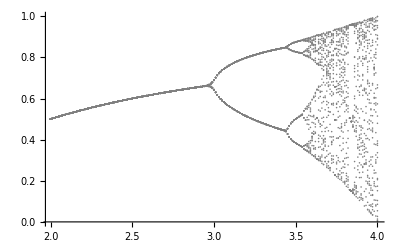

```mathematica
Clear[r,x];x0=0.1;
ziskejAtraktor[r_]:=(
dataL=RecurrenceTable[{x[n5] == r x[n5 - 1] (1 - x[n5 - 1]), x[0] == x0}, x, {n5, 0, 100}];
dataA=dataL[[-30;;Length[dataL]]];
Transpose[{Table[r,{i,1,Length[dataA]}],dataA}]
);
dataX=Table[ziskejAtraktor[r],{r,2,4,0.01}];
figX=ListPlot[Flatten[dataX,1],PlotStyle->Gray]
```

```mathematica
tA[];
T1 =AbsoluteTiming[dat1=ParallelTable[{ii,BoxCount1[fceX[ii,EnD1]]},{ii,2.01,4,step}];][[1]]
tB[];
```

3.26717

TIME 00:00:03 30  #  Start 00:59:24 Monday 10/09 / Konec 00:59:27 Monday 10/09

```mathematica
tA[];
T11 =AbsoluteTiming[dat11=ParallelTable[{ii,BoxCount1[fceX[ii,EnD1]]},{ii,2.01,4,step}];][[1]]
tB[];

tA[];
T111=AbsoluteTiming[dat111=ParallelTable[{ii,BoxCount1[fceX[ii,EnD2]]},{ii,2.01,4,step}];][[1]]
tB[];
```

0.386619

TIME 00:00:00 30  #  Start 00:59:27 Monday 10/09 / Konec 00:59:28 Monday 10/09

4.03918

TIME 00:00:04 30  #  Start 00:59:28 Monday 10/09 / Konec 00:59:32 Monday 10/09

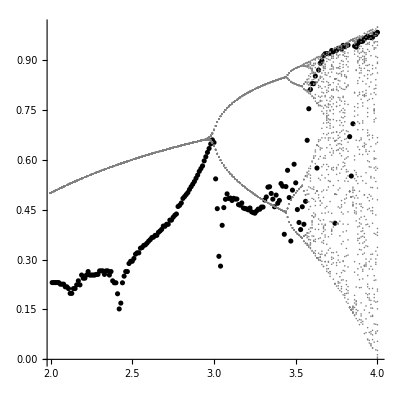

```mathematica
Show[{ListPlot[dat1,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

```mathematica
Show[{ListPlot[dat11,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

-Graphics-

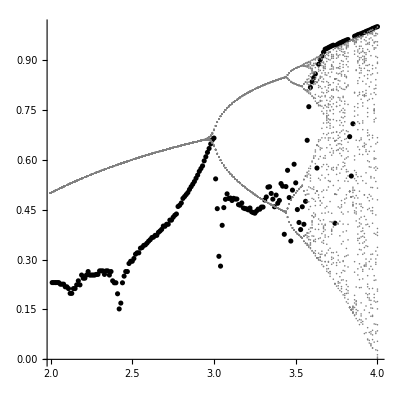

```mathematica
Show[{ListPlot[dat111,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

```mathematica
tA[];
T2=AbsoluteTiming[dat2=ParallelTable[{ii,corrDIMdim1[fceX[ii,EnD]]},{ii,2,4,step}];][[1]]
tB[];
```

1.34963

TIME 00:00:01 30  #  Start 00:59:32 Monday 10/09 / Konec 00:59:33 Monday 10/09

```mathematica
tA[];
T22=AbsoluteTiming[dat22=ParallelTable[{ii,corrDIMdim1[fceX[ii,EnD1]]},{ii,2,4,step}];][[1]]
tB[];
```

27.8619

TIME 00:00:27 30  #  Start 00:59:33 Monday 10/09 / Konec 01:00:01 Monday 10/09

```mathematica
tA[];
T222=AbsoluteTiming[dat222=ParallelTable[{ii,corrDIMdim1[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
```

38658.2

TIME 10:44:18 30  #  Start 01:00:01 Monday 10/09 / Konec 11:44:19 Monday 10/09

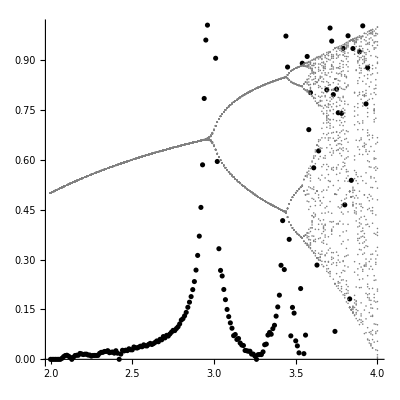

```mathematica
Show[{ListPlot[dat2,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

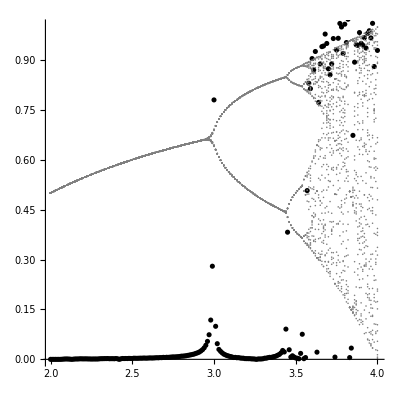

```mathematica
Show[{ListPlot[dat22,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

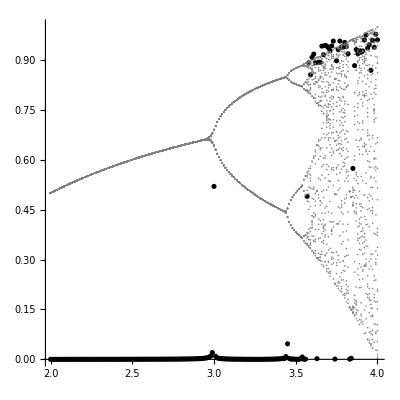

```mathematica
Show[{ListPlot[dat222,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

```mathematica
tA[];
T3 =AbsoluteTiming[dat3=ParallelTable[{ii,Lyapun2[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

5.81747

TIME 00:00:05 30  #  Start 11:44:20 Monday 10/09 / Konec 11:44:26 Monday 10/09

```mathematica
tA[];
T33=AbsoluteTiming[dat33=ParallelTable[{ii,Lyapun2[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

127.432

TIME 00:02:07 30  #  Start 11:44:26 Monday 10/09 / Konec 11:46:33 Monday 10/09

```mathematica
tA[];
T333=AbsoluteTiming[dat333=ParallelTable[{ii,Lyapun2[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

13358.9

TIME 03:42:36 30  #  Start 11:46:33 Monday 10/09 / Konec 15:29:10 Monday 10/09

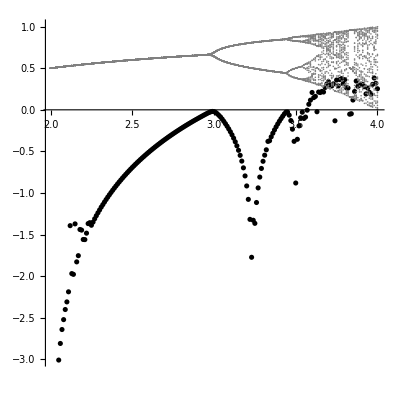

```mathematica
Show[{ListPlot[dat3,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{-3,1}}]
```

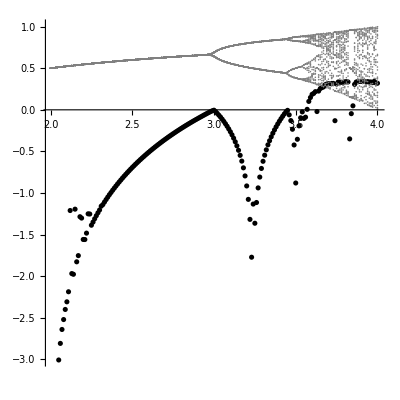

```mathematica
Show[{ListPlot[dat33,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{-3,1}}]
```

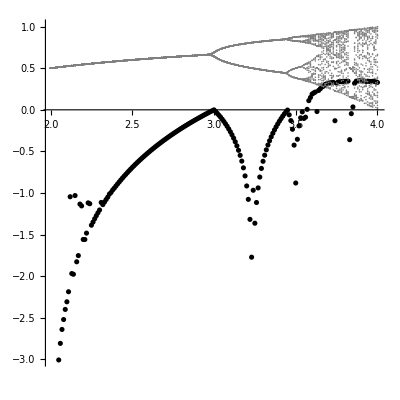

```mathematica
Show[{ListPlot[dat333,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{-3,1}}]
```

```mathematica
tA[];
T4 =AbsoluteTiming[dat4=ParallelTable[{ii,f1[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.459739

TIME 00:00:00 30  #  Start 15:29:12 Monday 10/09 / Konec 15:29:12 Monday 10/09

```mathematica
tA[];
T44 =AbsoluteTiming[dat44=ParallelTable[{ii,f1[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

6.45309

TIME 00:00:06 30  #  Start 15:29:12 Monday 10/09 / Konec 15:29:18 Monday 10/09

```mathematica
tA[];
T444 =AbsoluteTiming[dat444=ParallelTable[{ii,f1[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

498.156

TIME 00:08:18 30  #  Start 15:29:19 Monday 10/09 / Konec 15:37:37 Monday 10/09

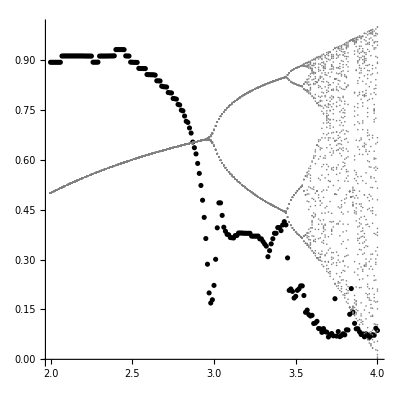

```mathematica
Show[{ListPlot[Table[Flatten[dat4[[i]]],{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

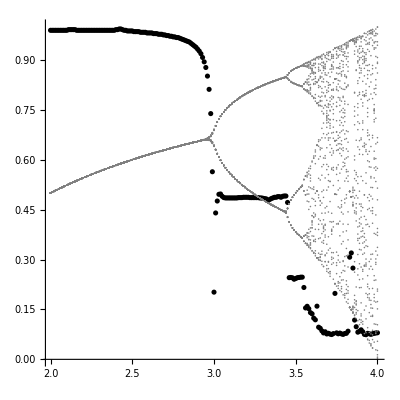

```mathematica
Show[{ListPlot[Table[Flatten[dat44[[i]]],{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

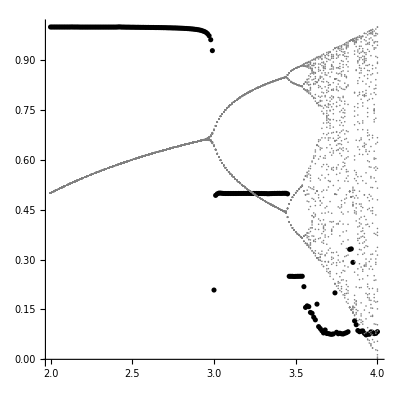

```mathematica
Show[{ListPlot[Table[Flatten[dat444[[i]]],{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

```mathematica
tA[];
T5 =AbsoluteTiming[dat5=ParallelTable[{ii,Rp1[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.589846

TIME 00:00:00 30  #  Start 15:37:37 Monday 10/09 / Konec 15:37:38 Monday 10/09

```mathematica
tA[];
T55 =AbsoluteTiming[dat55=ParallelTable[{ii,Rp1[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

6.14847

TIME 00:00:06 30  #  Start 15:37:38 Monday 10/09 / Konec 15:37:44 Monday 10/09

```mathematica
tA[];
T555=AbsoluteTiming[dat555=ParallelTable[{ii,Rp1[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

899.666

TIME 00:14:59 30  #  Start 15:37:44 Monday 10/09 / Konec 15:52:44 Monday 10/09

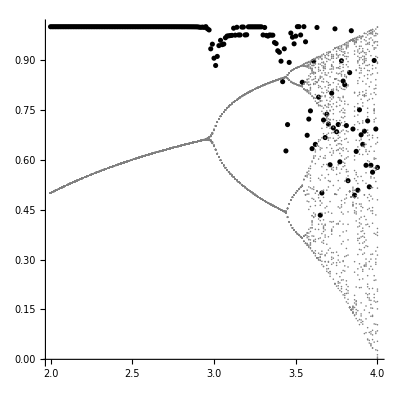

```mathematica
Show[{ListPlot[dat5B = Table[{dat5[[i]][[1]],dat5[[i]][[2]][[2]]},{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

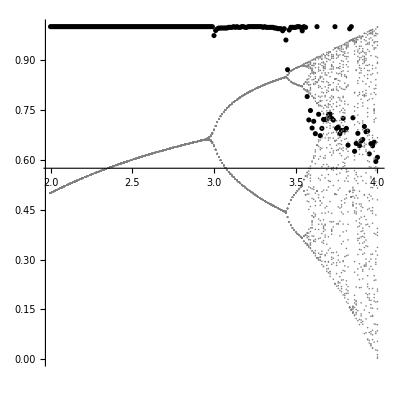

```mathematica
Show[{ListPlot[dat55B =Table[{dat55[[i]][[1]],dat55[[i]][[2]][[2]]},{i,1,Length[dat44]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

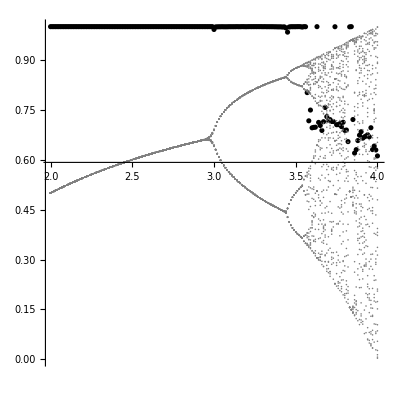

```mathematica
Show[{ListPlot[dat555B =Table[{dat555[[i]][[1]],dat555[[i]][[2]][[2]]},{i,1,Length[dat444]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

```mathematica
tA[];
T6 =AbsoluteTiming[dat6=ParallelTable[{ii,RpAl[fceX[ii,EnD]]},{ii,2.,4,step}];][[1]]
tB[];
```

0.210083

TIME 00:00:00 30  #  Start 15:52:45 Monday 10/09 / Konec 15:52:45 Monday 10/09

```mathematica
tA[];
T66=AbsoluteTiming[dat66=ParallelTable[{ii,RpAl[fceX[ii,EnD1]]},{ii,2.,4,step}];][[1]]
tB[];
```

7.06622

TIME 00:00:07 30  #  Start 15:52:45 Monday 10/09 / Konec 15:52:52 Monday 10/09

```mathematica
tA[];
T666=AbsoluteTiming[dat666=ParallelTable[{ii,RpAl[fceX[ii,EnD2]]},{ii,2.,4,step}];][[1]]
tB[];
```

1112.75

TIME 00:18:32 30  #  Start 15:52:52 Monday 10/09 / Konec 16:11:25 Monday 10/09

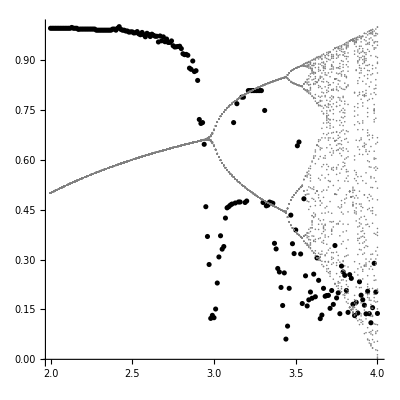

```mathematica
D63 =Table[{dat6[[i]][[1]],dat6[[i]][[2]][[3]]},{i,1,Length[dat4]}];

Show[{ListPlot[dat6C=Table[{dat6[[i]][[1]],dat6[[i]][[2]][[3]]/Max[D63]},{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]  (*Znormovane*)
```

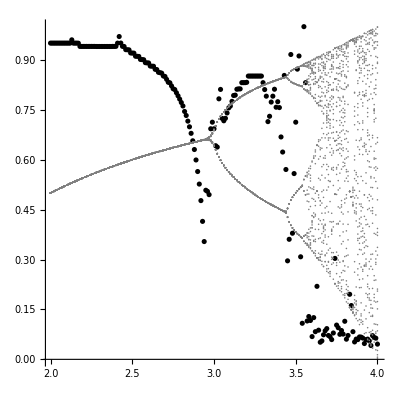

```mathematica
D64 =Table[{dat6[[i]][[1]],dat6[[i]][[2]][[4]]},{i,1,Length[dat4]}];

Show[{ListPlot[dat6D =Table[{dat6[[i]][[1]],dat6[[i]][[2]][[4]]/Max[D64]},{i,1,Length[dat4]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}] (*Znormovane*)
```

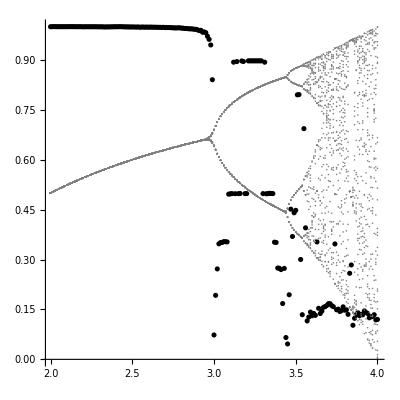

```mathematica
D663 =Table[{dat66[[i]][[1]],dat66[[i]][[2]][[3]]},{i,1,Length[dat44]}];

Show[{ListPlot[dat66C=Table[{dat66[[i]][[1]],dat66[[i]][[2]][[3]]/Max[D663]},{i,1,Length[dat44]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]  (*Znormovane*)
```

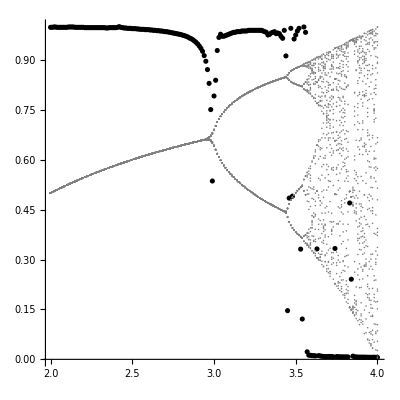

```mathematica
D664 =Table[{dat66[[i]][[1]],dat66[[i]][[2]][[4]]},{i,1,Length[dat44]}];

Show[{ListPlot[dat66D =Table[{dat66[[i]][[1]],dat66[[i]][[2]][[4]]/Max[D664]},{i,1,Length[dat44]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}] (*Znormovane*)
```

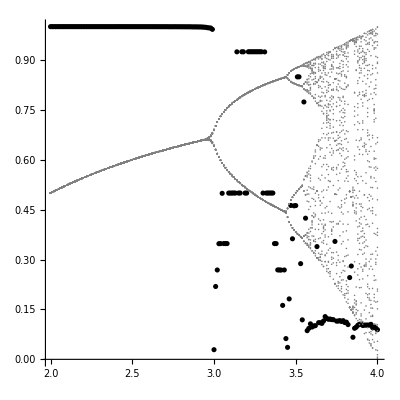

```mathematica
D6663 =Table[{dat666[[i]][[1]],dat666[[i]][[2]][[3]]},{i,1,Length[dat444]}];

Show[{ListPlot[dat666C =Table[{dat666[[i]][[1]],dat666[[i]][[2]][[3]]/Max[D6663]},{i,1,Length[dat444]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]  (*Znormovane*)
```

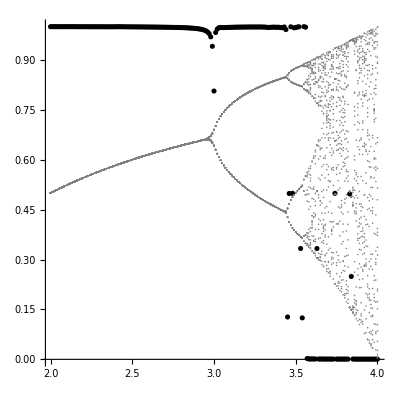

```mathematica
D6664 =Table[{dat666[[i]][[1]],dat666[[i]][[2]][[4]]},{i,1,Length[dat444]}];

Show[{ListPlot[dat666D = Table[{dat666[[i]][[1]],dat666[[i]][[2]][[4]]/Max[D6664]},{i,1,Length[dat444]}],PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}] (*Znormovane*)
```

```mathematica
c3100=Import["c3100.wmlf"]
c31000=Import["c31000.wmlf"]
c310000=Import["c310000.wmlf"]
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierFunction[…]

```mathematica
tA[];
T7=AbsoluteTiming[dat7=ParallelTable[{ii,c3100[fceX[ii,100],"Probabilities"][[2]]},{ii,2.,4,step}];][[1]]
tB[];

tA[];
T77=AbsoluteTiming[dat77=ParallelTable[{ii,c31000[fceX[ii,1000],"Probabilities"][[2]]},{ii,2.,4,step}];][[1]]
tB[];

tA[];
T777=AbsoluteTiming[dat777=ParallelTable[{ii,c310000[fceX[ii,10000],"Probabilities"][[2]]},{ii,2.,4,step}];][[1]]
tB[];
```

8.26507

TIME 00:00:08 30  #  Start 16:11:35 Monday 10/09 / Konec 16:11:43 Monday 10/09

3.59058

TIME 00:00:03 30  #  Start 16:11:43 Monday 10/09 / Konec 16:11:47 Monday 10/09

20.4494

TIME 00:00:20 30  #  Start 16:11:47 Monday 10/09 / Konec 16:12:07 Monday 10/09

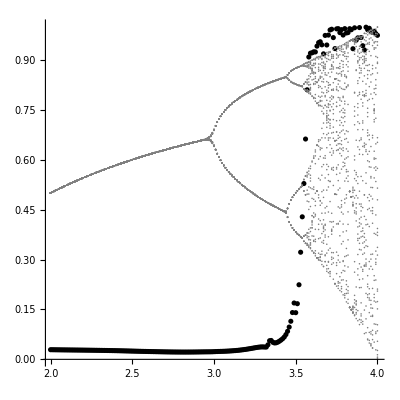

```mathematica
Show[{ListPlot[dat7,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

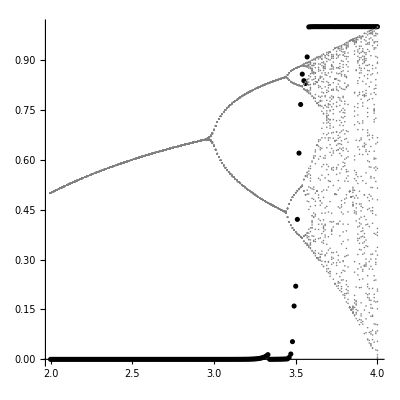

```mathematica
Show[{ListPlot[dat77,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

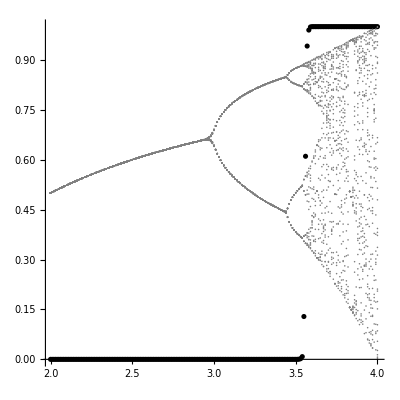

```mathematica
Show[{ListPlot[dat777,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

```mathematica
TB1={{InputField[Dynamic[{LogisticMap,konec EnD ,krok step}]]},{InputField[Dynamic[BoxCount T1]]},
{InputField[Dynamic[CorrDim T2]]},
{InputField[Dynamic[Lyapun T3]]},
{InputField[Dynamic[RQAf1 T4]]},
{InputField[Dynamic[RQARRDET T5]]},
{InputField[Dynamic[RQARRDETLENTR T6]]}
} //MatrixForm
```

(





)

```mathematica
TB2 //MatrixForm
```

TB2

```mathematica
TB3={{InputField[Deploy[TextCell["Method / Length"]],FieldSize->10],InputField[EnD,FieldSize->10],InputField[EnD1,FieldSize->10]},{InputField[Deploy[TextCell["Boxcount"]],FieldSize->10],InputField[T1,FieldSize->10],InputField[T11,FieldSize->10]},{InputField[Deploy[TextCell["Corr. dim."]],FieldSize->10],InputField[T2,FieldSize->10],InputField[T22,FieldSize->10]},{InputField[Deploy[TextCell["Lyap. exp."]],FieldSize->10],InputField[T3,FieldSize->10],InputField[T33,FieldSize->10]},{InputField[Deploy[TextCell["RQA RR"]],FieldSize->10],InputField[T4,FieldSize->10],InputField[T44,FieldSize->10]},{InputField[Deploy[TextCell["RQA DET"]],FieldSize->10],InputField[T5,FieldSize->10],InputField[T55,FieldSize->10]},{InputField[Deploy[TextCell["RQA ENTR"]],FieldSize->10],InputField[T6,FieldSize->10],InputField[T66,FieldSize->10]},{InputField[Deploy[TextCell["RQA L"]],FieldSize->10],InputField[T6,FieldSize->10],InputField[T66,FieldSize->10]}} //MatrixForm
```

( |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | 
 |  | )

```mathematica
Export["TB3.png",TB3]
```

TB3.png

```mathematica
TB4={{InputField[Deploy[TextCell["Method / Length"]],FieldSize->10],InputField[EnD,FieldSize->10],InputField[EnD1,FieldSize->10],InputField[EnD2,FieldSize->10]},{InputField[Deploy[TextCell["Boxcount"]],FieldSize->10],InputField[T1,FieldSize->10],InputField[T11,FieldSize->10],InputField[T111,FieldSize->10]},{InputField[Deploy[TextCell["Corr. dim."]],FieldSize->10],InputField[T2,FieldSize->10],InputField[T22,FieldSize->10],InputField[T222,FieldSize->10]},{InputField[Deploy[TextCell["Lyap. exp."]],FieldSize->10],InputField[T3,FieldSize->10],InputField[T33,FieldSize->10],InputField[T333,FieldSize->10]},{InputField[Deploy[TextCell["RQA RR"]],FieldSize->10],InputField[T4,FieldSize->10],InputField[T44,FieldSize->10],InputField[T444,FieldSize->10]},{InputField[Deploy[TextCell["RQA DET"]],FieldSize->10],InputField[T5,FieldSize->10],InputField[T55,FieldSize->10],InputField[T555,FieldSize->10]},{InputField[Deploy[TextCell["RQA ENTR"]],FieldSize->10],InputField[T6,FieldSize->10],InputField[T66,FieldSize->10],InputField[T666,FieldSize->10]},{InputField[Deploy[TextCell["RQA L"]],FieldSize->10],InputField[T6,FieldSize->10],InputField[T66,FieldSize->10],InputField[T666,FieldSize->10]},{InputField[Deploy[TextCell["Machine learning"]],FieldSize->10],InputField[T7,FieldSize->10],InputField[T77,FieldSize->10],InputField[T777,FieldSize->10]}} //MatrixForm
```

( |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | 
 |  |  | )

```mathematica
Export["TB4.png",TB4]
```

TB4.png

```mathematica
Export["dat1.dat",dat1,"Table"];Export["dat11.dat",dat11,"Table"];Export["dat111.dat",dat111,"Table"];

Export["dat2.dat",dat2,"Table"];Export["dat22.dat",dat22,"Table"];Export["dat222.dat",dat222,"Table"];

Export["dat3.dat",dat3,"Table"];Export["dat33.dat",dat33,"Table"];Export["dat333.dat",dat333,"Table"];

Export["dat4.dat",dat4,"Table"];Export["dat44.dat",dat44,"Table"];Export["dat444.dat",dat444,"Table"];

Export["dat5B.dat",dat5B,"Table"];Export["dat55B.dat",dat55B,"Table"];Export["dat5B.dat",dat555B,"Table"];

Export["dat6C.dat",dat6C,"Table"];Export["dat66C.dat",dat66C,"Table"];Export["dat666C.dat",dat666C,"Table"];

Export["dat6D.dat",dat6D,"Table"];Export["dat66D.dat",dat66D,"Table"];Export["dat666D.dat",dat666D,"Table"];
```

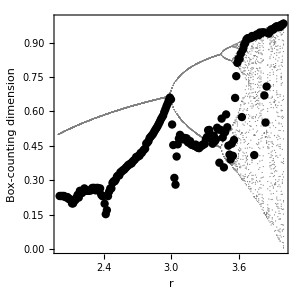

```mathematica
pic1=Show[{figX,ListPlot[dat1,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Box-counting dimension"}]
```

```mathematica
pic11=Show[{figX,ListPlot[dat11,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Box-counting dimension"}]
```

-Graphics-

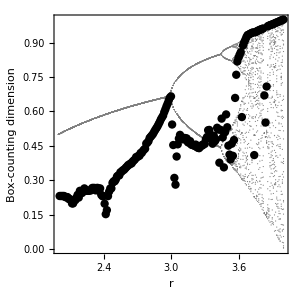

```mathematica
pic111=Show[{figX,ListPlot[dat111,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Box-counting dimension"}]
```

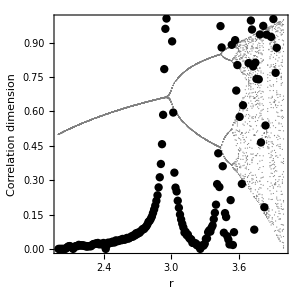

```mathematica
pic2=Show[{figX,ListPlot[dat2,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Correlation dimension"}]
```

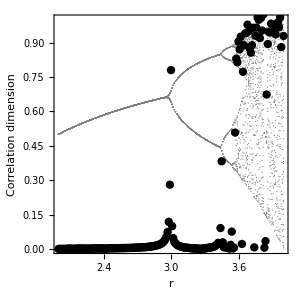

```mathematica
pic22=Show[{figX,ListPlot[dat22,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Correlation dimension"}]
```

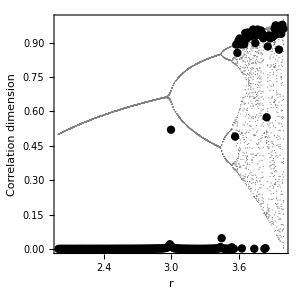

```mathematica
pic222=Show[{figX,ListPlot[dat222,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Correlation dimension"}]
```

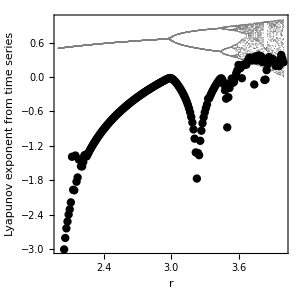

```mathematica
pic3=Show[{figX,ListPlot[dat3,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Lyapunov exponent from time series"}]
```

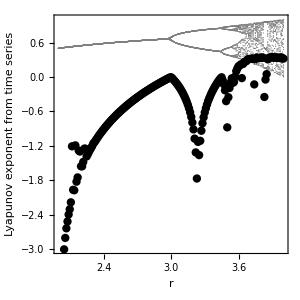

```mathematica
pic33=Show[{figX,ListPlot[dat33,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Lyapunov exponent from time series"}]
```

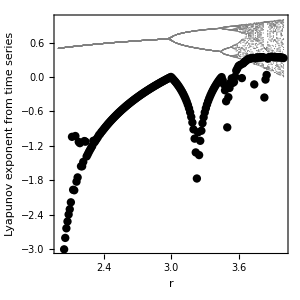

```mathematica
pic333=Show[{figX,ListPlot[dat333,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Lyapunov exponent from time series"}]
```

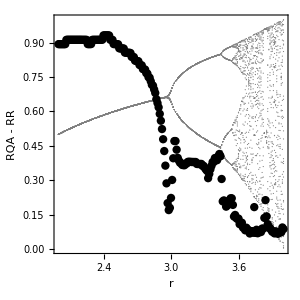

```mathematica
pic4=Show[{figX,ListPlot[dat4,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - RR"}]
```

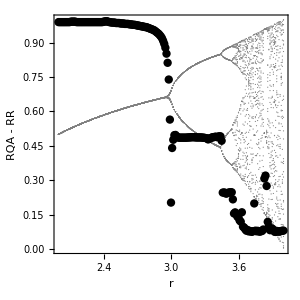

```mathematica
pic44=Show[{figX,ListPlot[dat44,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - RR"}]
```

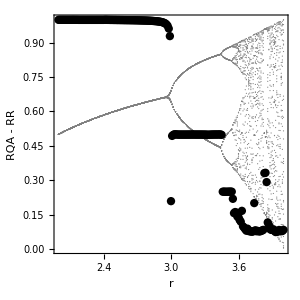

```mathematica
pic444=Show[{figX,ListPlot[dat444,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - RR"}]
```

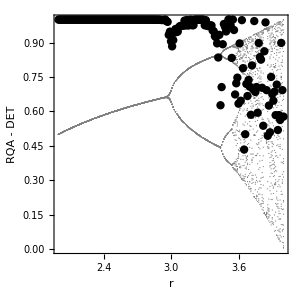

```mathematica
pic5=Show[{figX,ListPlot[dat5B,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - DET"}]
```

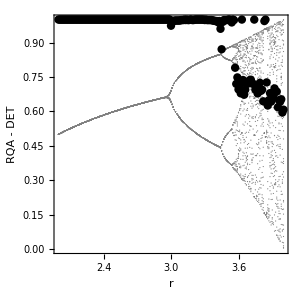

```mathematica
pic55=Show[{figX,ListPlot[dat55B,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - DET"}]
```

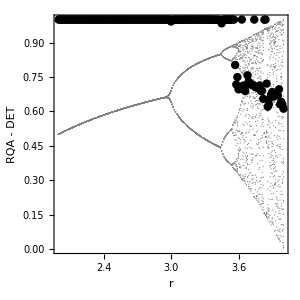

```mathematica
pic555=Show[{figX,ListPlot[dat555B,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - DET"}]
```

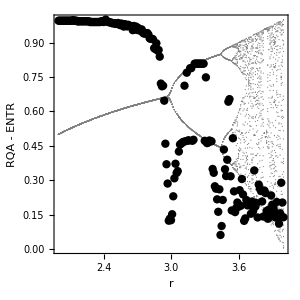

```mathematica
pic6=Show[{figX,ListPlot[dat6C,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - ENTR"}]
```

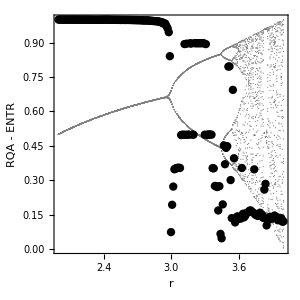

```mathematica
pic66=Show[{figX,ListPlot[dat66C,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - ENTR"}]
```

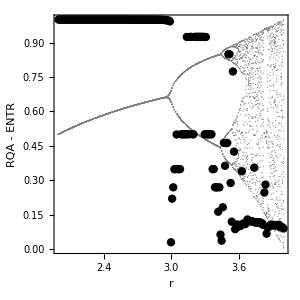

```mathematica
pic666=Show[{figX,ListPlot[dat666C,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - ENTR"}]
```

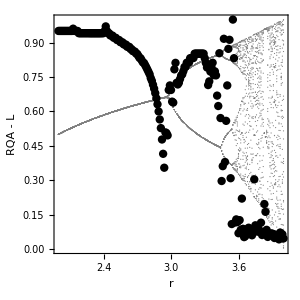

```mathematica
pic7=Show[{figX,ListPlot[dat6D,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - L"}]
```

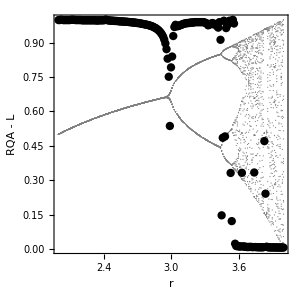

```mathematica
pic77=Show[{figX,ListPlot[dat66D,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - L"}]
```

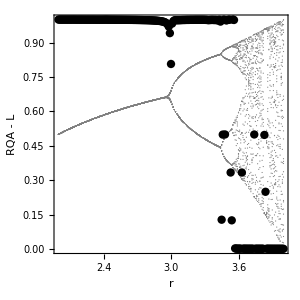

```mathematica
pic777=Show[{figX,ListPlot[dat666D,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","RQA - L"}]
```

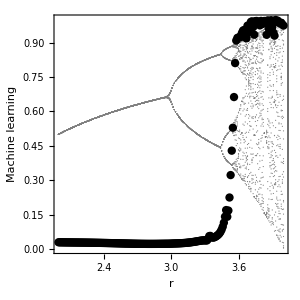

```mathematica
pic8=Show[{figX,ListPlot[dat7,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Machine learning"}]
```

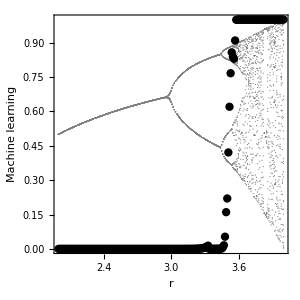

```mathematica
pic88=Show[{figX,ListPlot[dat77,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Machine learning"}]
```

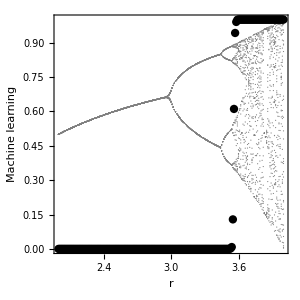

```mathematica
pic888=Show[{figX,ListPlot[dat777,PlotStyle->{{PointSize[0.02],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Machine learning"}]
```

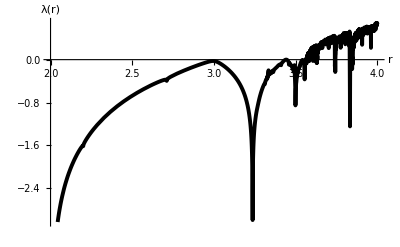

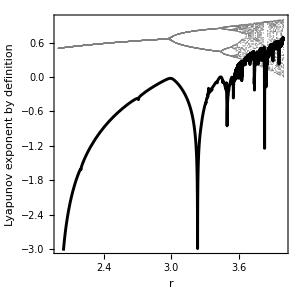

```mathematica
λ[r_]:=Module[{f,l},f[x_]:=r x (1-x);
l[x_]:=Log[Abs[r (1-2 x)]];
Mean[l[NestList[f,0.1,1*^2]]]];
pick=Plot[λ[r],{r,2,4},PlotStyle->{Thickness[.007],Black},AxesLabel->{"r","λ(r)"}]

picL=Show[{figX,pick},AspectRatio->1,PlotRange->{{2,4},{-3,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","Lyapunov exponent by definition"}]
```

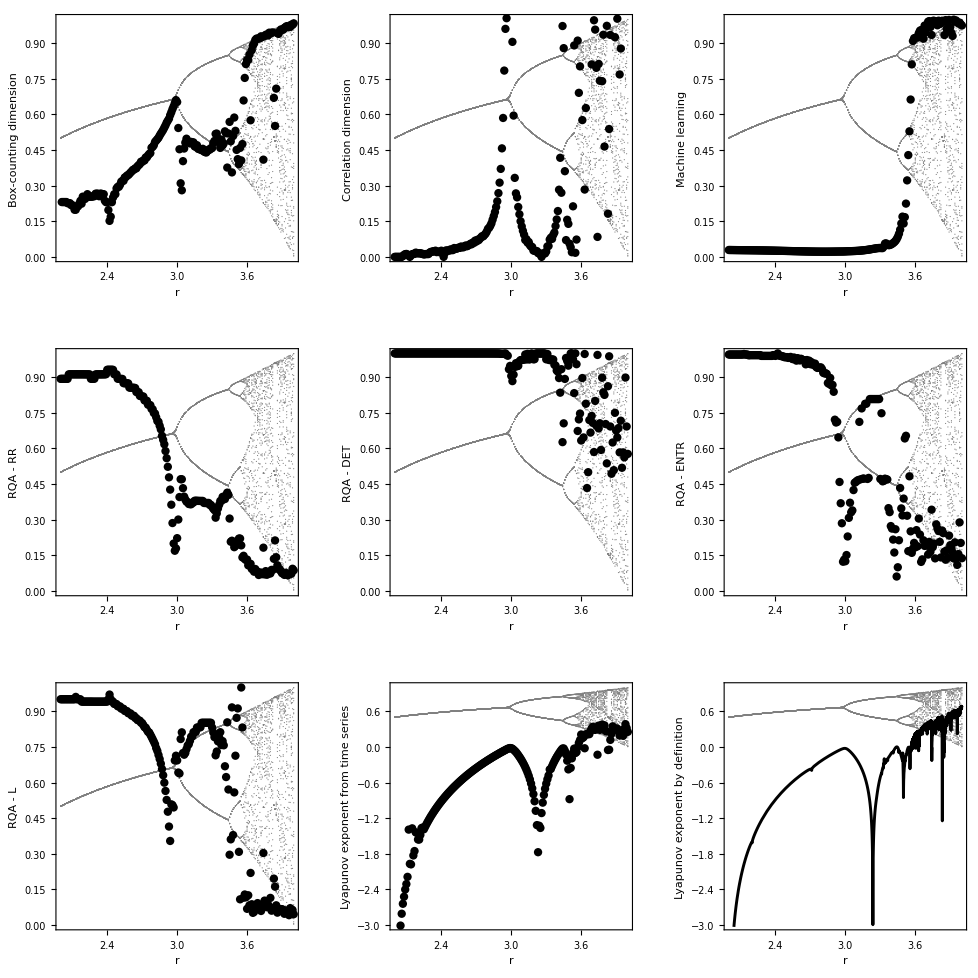

PPic1.png

```mathematica
PPic1=GraphicsGrid[{{pic1,pic2,pic8},{pic4,pic5,pic6},{pic7,pic3,picL}}]
 Export["PPic1.png",PPic1]
```

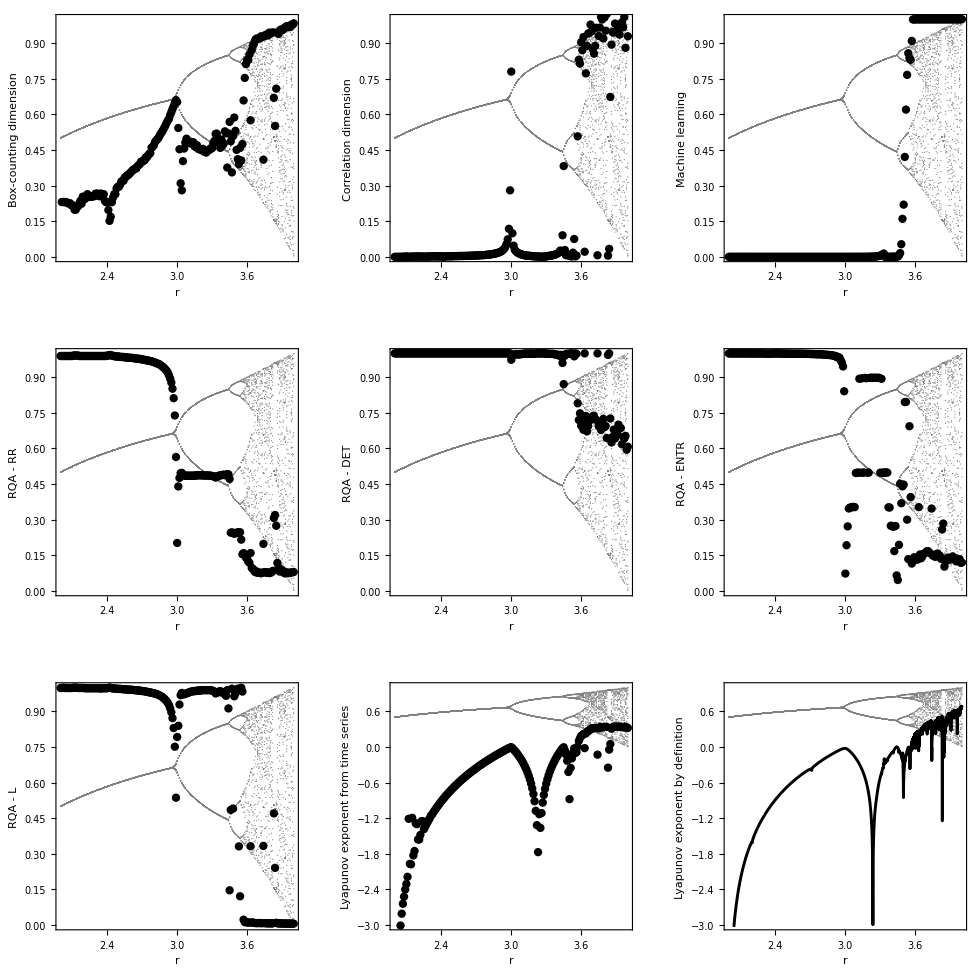

PPic2.png

```mathematica
PPic2=GraphicsGrid[{{pic11,pic22,pic88},{pic44,pic55,pic66},{pic77,pic33,picL}}]
 Export["PPic2.png",PPic2]
```

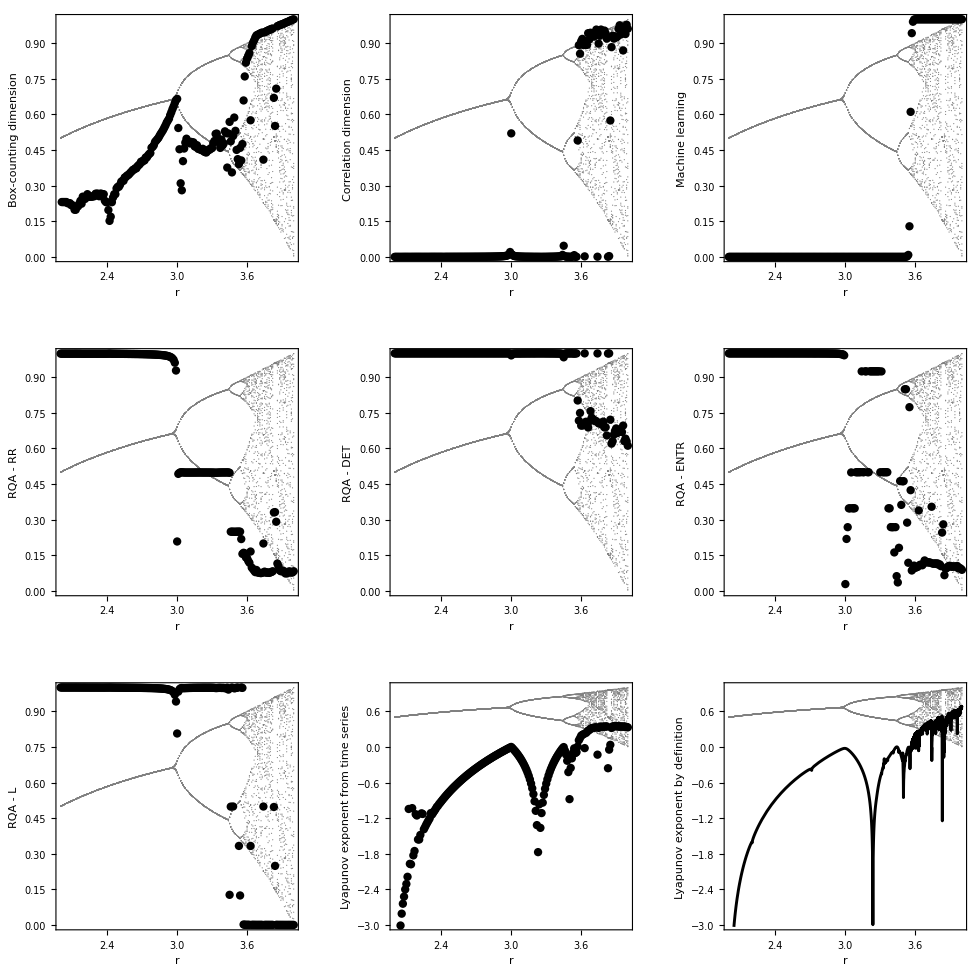

PPic3.png

```mathematica
PPic3=GraphicsGrid[{{pic111,pic222,pic888},{pic444,pic555,pic666},{pic777,pic333,picL}}] 
Export["PPic3.png",PPic3]
```

```mathematica
TRA2[da_]:= Flatten[1-{da- Min[da]}/Max[{da- Min[da]}],1];
```

```mathematica
TRA1[da_]:= Flatten[{da- Min[da]}/Max[{da- Min[da]}],1];
```

```mathematica
dat444;
```

```mathematica
dat666D;
dat666C;
```

```mathematica
dat555B;
```

```mathematica
dat333;
```

```mathematica
dat222;
```

```mathematica
dat111;
```

```mathematica
D1 = Take[Table[dat111[[i]][[2]],{i,1,Length[dat111]}],-200];D2= Take[Table[dat222[[i]][[2]],{i,1,Length[dat222]}],-200];D3 =Take[ Table[dat333[[i]][[2]],{i,1,Length[dat333]}],-200];D4=Take[ Table[dat444[[i]][[2]],{i,1,Length[dat444]}],-200];D5 =Take[ Table[dat555B[[i]][[2]],{i,1,Length[dat555]}],-200];D6 = Take[Table[dat666C[[i]][[2]],{i,1,Length[dat666]}],-200];D7 =Take[ Table[dat666D[[i]][[2]],{i,1,Length[dat777]}],-200];
```

```mathematica
TRST = TRA1[D1]+TRA1[D2] + TRA1[D3] + TRA2[D4] + TRA2[D5] + TRA2[D6] + TRA2[D7]
```

{0.0939242,0.259726,0.333067,0.390779,0.424984,0.459071,0.492463,0.516283,0.531116,0.549402,0.567219,0.777816,0.59341,0.609053,0.797602,0.652227,0.681364,0.790732,0.821169,0.72966,0.72957,0.756008,0.840906,0.826411,0.774986,0.782527,0.790448,0.800065,0.807047,0.826267,0.844275,0.839178,0.833059,0.85139,0.857186,0.849648,0.865912,0.839071,0.836461,0.841561,0.807271,0.757535,0.783653,0.860636,0.888675,0.909672,0.913948,0.946824,0.959035,0.963073,0.976962,0.996401,1.00508,1.0088,1.02918,1.035,1.04621,1.05194,1.06142,1.0718,1.08077,1.09151,1.09631,1.10608,1.10923,1.12285,1.13116,1.13989,1.15494,1.15698,1.1674,1.17052,1.18823,1.19131,1.20425,1.21406,1.22168,1.25117,1.25853,1.26965,1.28875,1.29848,1.30851,1.31872,1.33294,1.34587,1.3582,1.37107,1.38613,1.40146,1.41865,1.43338,1.44855,1.47275,1.49536,1.52263,1.55262,1.59774,1.69263,4.13725,2.76714,2.586,2.32256,2.28149,2.26564,2.47914,2.50278,2.51561,2.3359,2.33006,2.31373,2.31292,2.30177,1.85408,2.2612,2.24687,1.80296,1.769,2.18509,2.1599,1.68634,1.64513,1.541,1.6985,1.61738,1.67435,1.71643,1.74227,1.77037,2.22583,1.82843,2.28999,2.33771,2.3489,2.33381,2.32196,2.45962,2.50916,2.5689,2.58594,2.65365,2.76201,2.48296,2.89204,3.9189,3.47265,2.5098,3.27395,2.72802,2.56884,2.17847,2.1638,3.40517,3.89092,2.28616,2.80016,5.38533,6.15094,6.11123,6.34324,6.37635,6.37189,3.67548,6.38675,6.43699,6.55139,6.47291,6.38325,6.47377,6.50399,6.49398,6.52914,6.5471,3.23866,6.50883,6.55387,6.57413,6.58502,6.55189,6.63556,6.62011,6.69432,3.47321,3.60839,5.62478,6.72929,6.76841,6.70221,6.67378,6.64121,6.70056,6.73303,6.74889,6.69928,6.72833,6.57102,6.84766,6.80264,6.87702,6.90616}

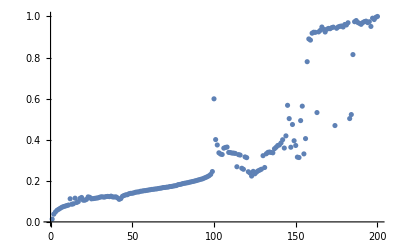

```mathematica
ListPlot[CH =TRST/ Max[TRST]]
```

```mathematica
LM=Take[ParallelTable[fceX[ii,EnD2],{ii,2.,4,0.01}],-200];


TTR1 = Table[LM [[i]] -> CH[[i]],{i,1,200}];
FIN  =RandomSample[TTR1,50];
```

```mathematica
p1 = Predict[FIN,Method->"DecisionTree"]; p2= Predict[FIN,Method->"NeuralNetwork"]; p3 = Predict[FIN,Method->"LinearRegression"]; p4 = Predict[FIN,Method->"RandomForest"]; p5 = Predict[FIN,Method->"GaussianProcess"]; p6 = Predict[FIN,Method->"NearestNeighbors"]; p7 = Predict[FIN,Method->"GradientBoostedTrees"];
```

```mathematica
tA[];
T777=AbsoluteTiming[dat777=ParallelTable[{ii,p1[fceX[ii,EnD2]]},{ii,2.01,4,step}];][[1]]
tB[];
```

18.0905

TIME 00:00:18 30  #  Start 23:45:09 Monday 10/09 / Konec 23:45:27 Monday 10/09

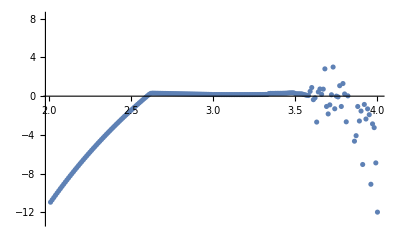

```mathematica
ListPlot[dat777]
```

```mathematica
tA[];
TM1=AbsoluteTiming[datm1=ParallelTable[{ii,p1[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM2=AbsoluteTiming[datm2=ParallelTable[{ii,p2[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM3=AbsoluteTiming[datm3=ParallelTable[{ii,p3[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM4=AbsoluteTiming[datm4=ParallelTable[{ii,p4[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM5=AbsoluteTiming[datm5=ParallelTable[{ii,p5[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM6=AbsoluteTiming[datm6=ParallelTable[{ii,p6[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
tA[];
TM7=AbsoluteTiming[datm7=ParallelTable[{ii,p7[fceX[ii,EnD2]]},{ii,2,4,step}];][[1]]
tB[];
```

9.93031

TIME 00:00:09 30  #  Start 00:04:13 Tuesday 11/09 / Konec 00:04:23 Tuesday 11/09

13.4975

TIME 00:00:13 30  #  Start 00:04:23 Tuesday 11/09 / Konec 00:04:37 Tuesday 11/09

9.94708

TIME 00:00:09 30  #  Start 00:04:37 Tuesday 11/09 / Konec 00:04:47 Tuesday 11/09

10.6386

TIME 00:00:10 30  #  Start 00:04:47 Tuesday 11/09 / Konec 00:04:57 Tuesday 11/09

12.046

TIME 00:00:12 30  #  Start 00:04:57 Tuesday 11/09 / Konec 00:05:09 Tuesday 11/09

10.5347

TIME 00:00:10 30  #  Start 00:05:09 Tuesday 11/09 / Konec 00:05:20 Tuesday 11/09

8.09628

TIME 00:00:08 30  #  Start 00:05:20 Tuesday 11/09 / Konec 00:05:28 Tuesday 11/09

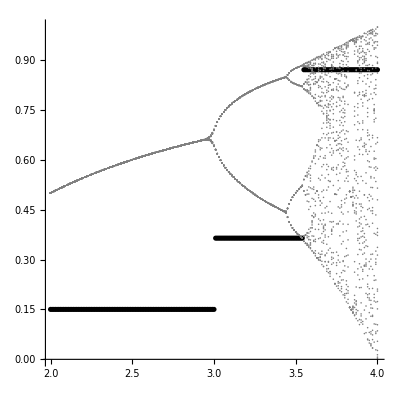

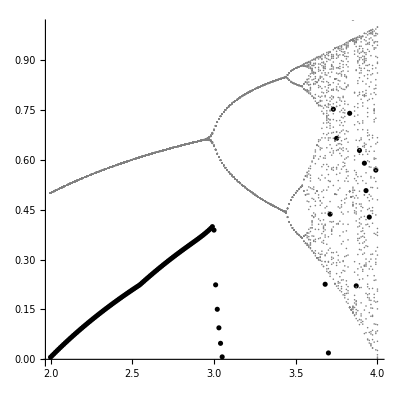

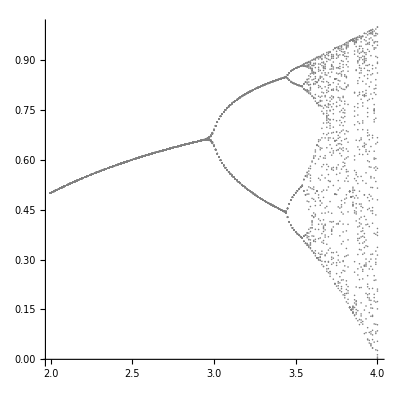

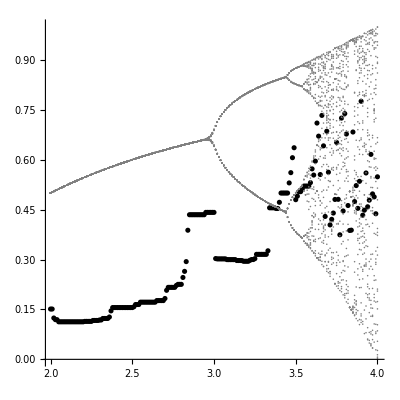

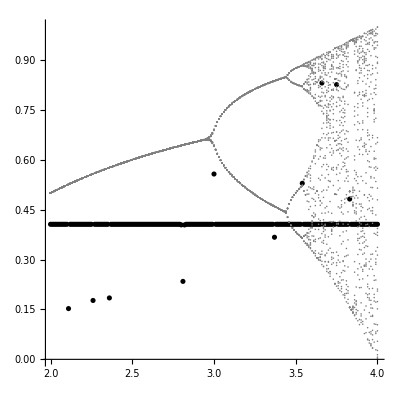

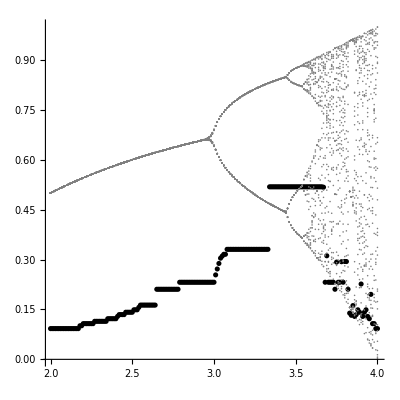

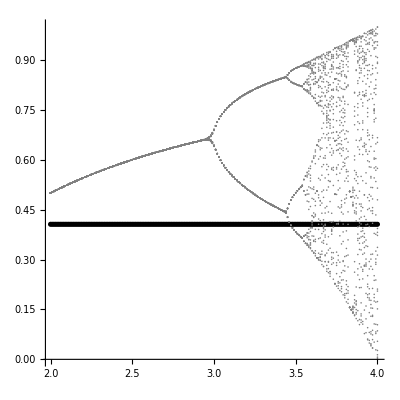

```mathematica
PM1 =Show[{ListPlot[datm1,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
PM2 =Show[{ListPlot[datm2,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
PM3=Show[{ListPlot[datm3,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
PM4=Show[{ListPlot[datm4,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
PM5 =Show[{ListPlot[datm5,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
PM6 =Show[{ListPlot[datm6,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
PM7 =Show[{ListPlot[datm7,PlotStyle->Black],figX},AspectRatio->1,PlotRange->{{2.,4},{0,1}}]
```

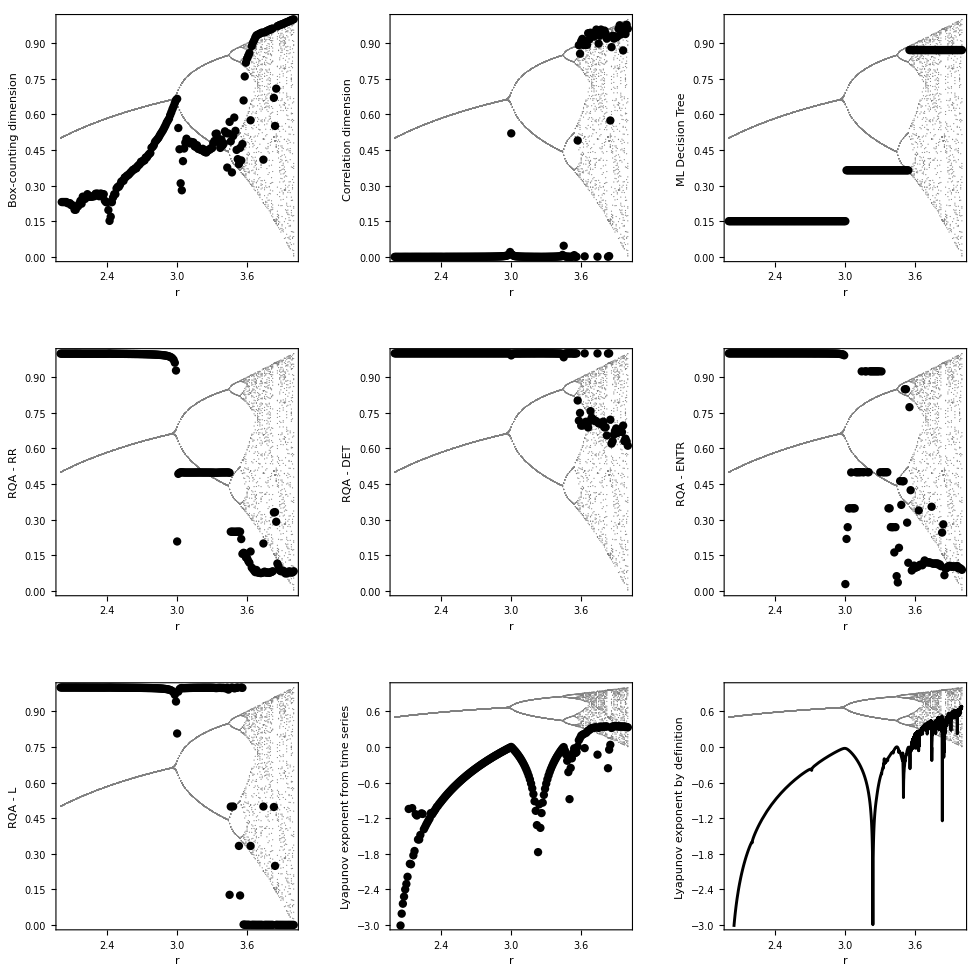

PPic1m.png

```mathematica
PPic1m=GraphicsGrid[{{pic111,pic222,picm1},{pic444,pic555,pic666},{pic777,pic333,picL}}] 
Export["PPic1m.png",PPic1m]
```

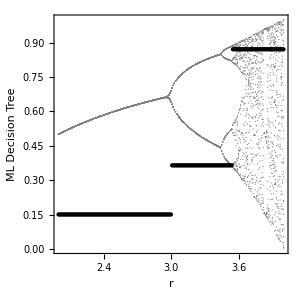

```mathematica
picm1=Show[{figX,ListPlot[datm1,PlotStyle->{{PointSize[0.01],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Decision Tree"}]
```

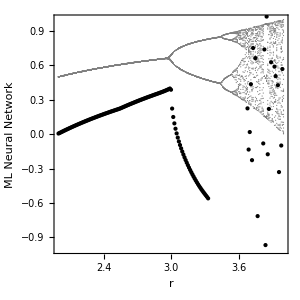

```mathematica
picm2=Show[{figX,ListPlot[datm2,PlotStyle->{{PointSize[0.01],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-1,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Neural Network"}]
```

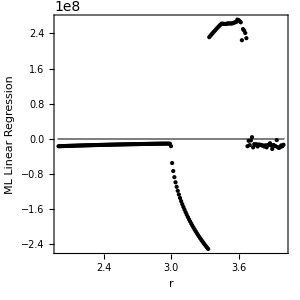

```mathematica
picm3=Show[{figX,ListPlot[datm3,PlotStyle->{{PointSize[0.01],Black}}]},AspectRatio->1,PlotRange->{{2,4},{-2.5057855388011646*^8,2.71450547162582*^8}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Linear Regression"}]
```

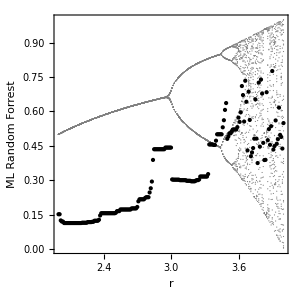

```mathematica
picm4=Show[{figX,ListPlot[datm4,PlotStyle->{{PointSize[0.01],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Random Forrest"}]
```

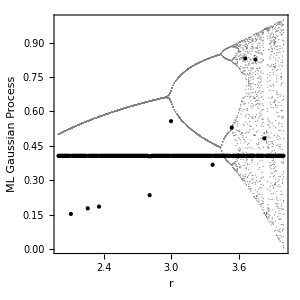

```mathematica
picm5=Show[{figX,ListPlot[datm5,PlotStyle->{{PointSize[0.01],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Gaussian Process"}]
```

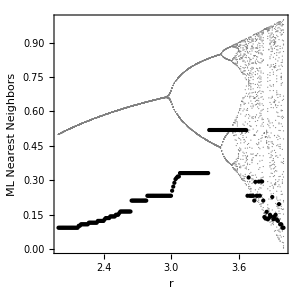

```mathematica
picm6=Show[{figX,ListPlot[datm6,PlotStyle->{{PointSize[0.01],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Nearest Neighbors"}]
```

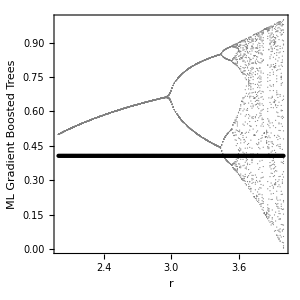

```mathematica
picm7=Show[{figX,ListPlot[datm7,PlotStyle->{{PointSize[0.01],Black}}]},AspectRatio->1,PlotRange->{{2,4},{0,1}},ImageSize->300,BaseStyle->15,Frame->True,FrameLabel->{"r","ML  Gradient Boosted Trees"}]
```

```mathematica
PPic2m=GraphicsGrid[{{pic111,pic222,picm1},{pic444,pic555,pic666},{pic777,pic333,picL},{picm2,picm3,picm4},{picm5,picm6,picm6}}] ;
Export["PPic2m.png",PPic2m];
```

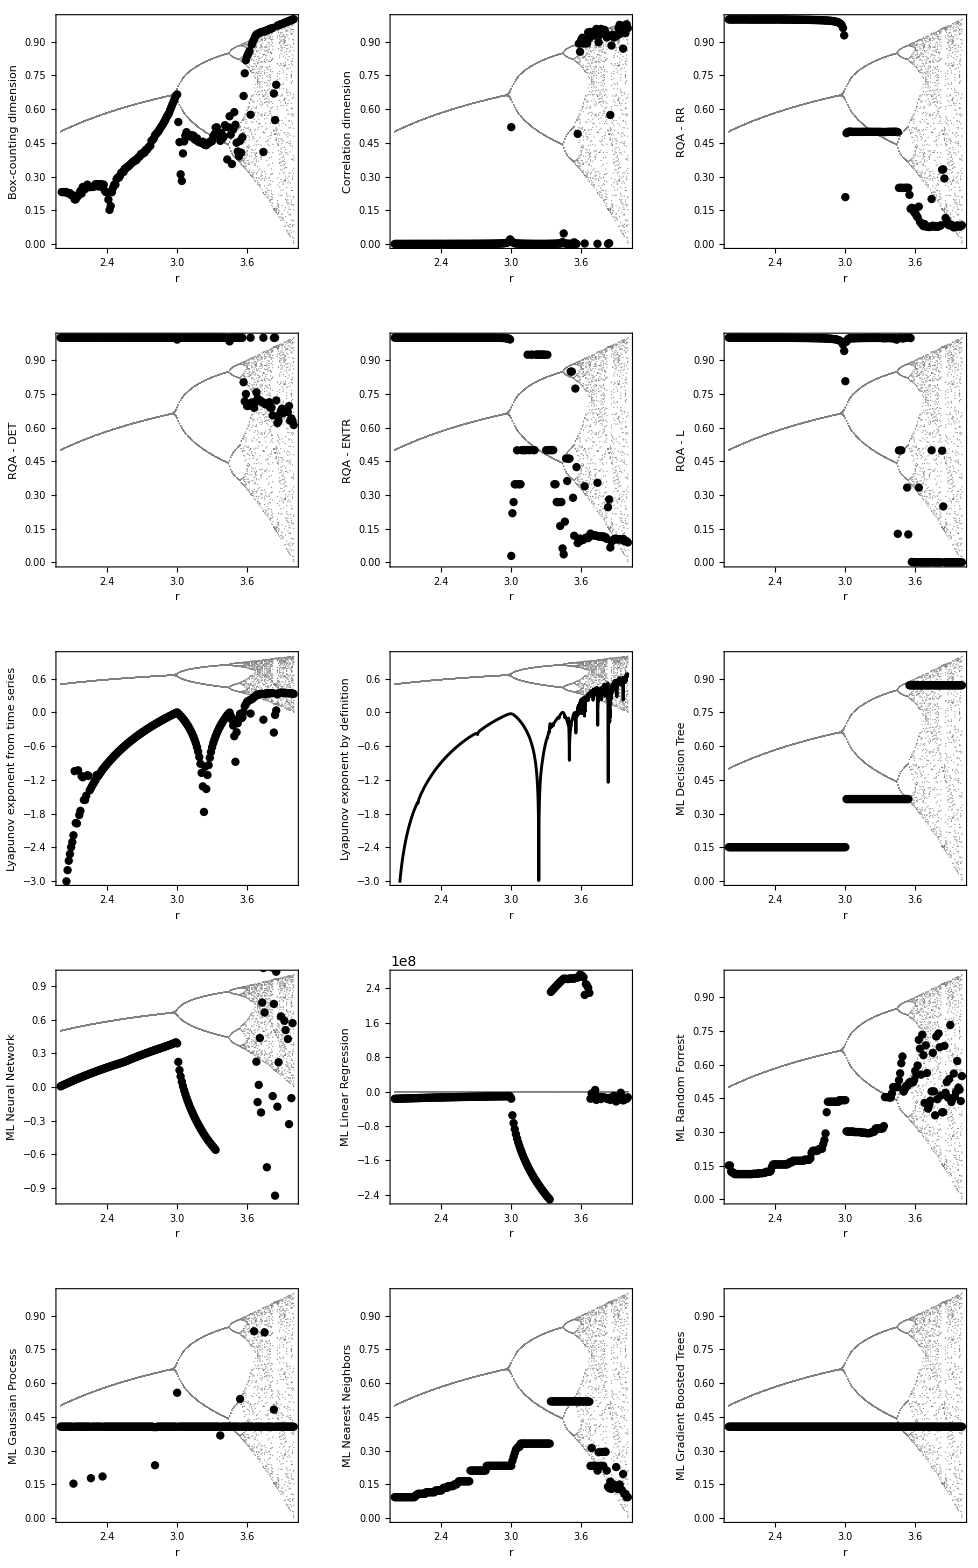

```mathematica
PPic3m=GraphicsGrid[{{pic111,pic222,pic444},{pic555,pic666,pic777},{pic333,picL,picm1},{picm2,picm3,picm4},{picm5,picm6,picm7}}] 
Export["PPic3m.png",PPic3m];
```

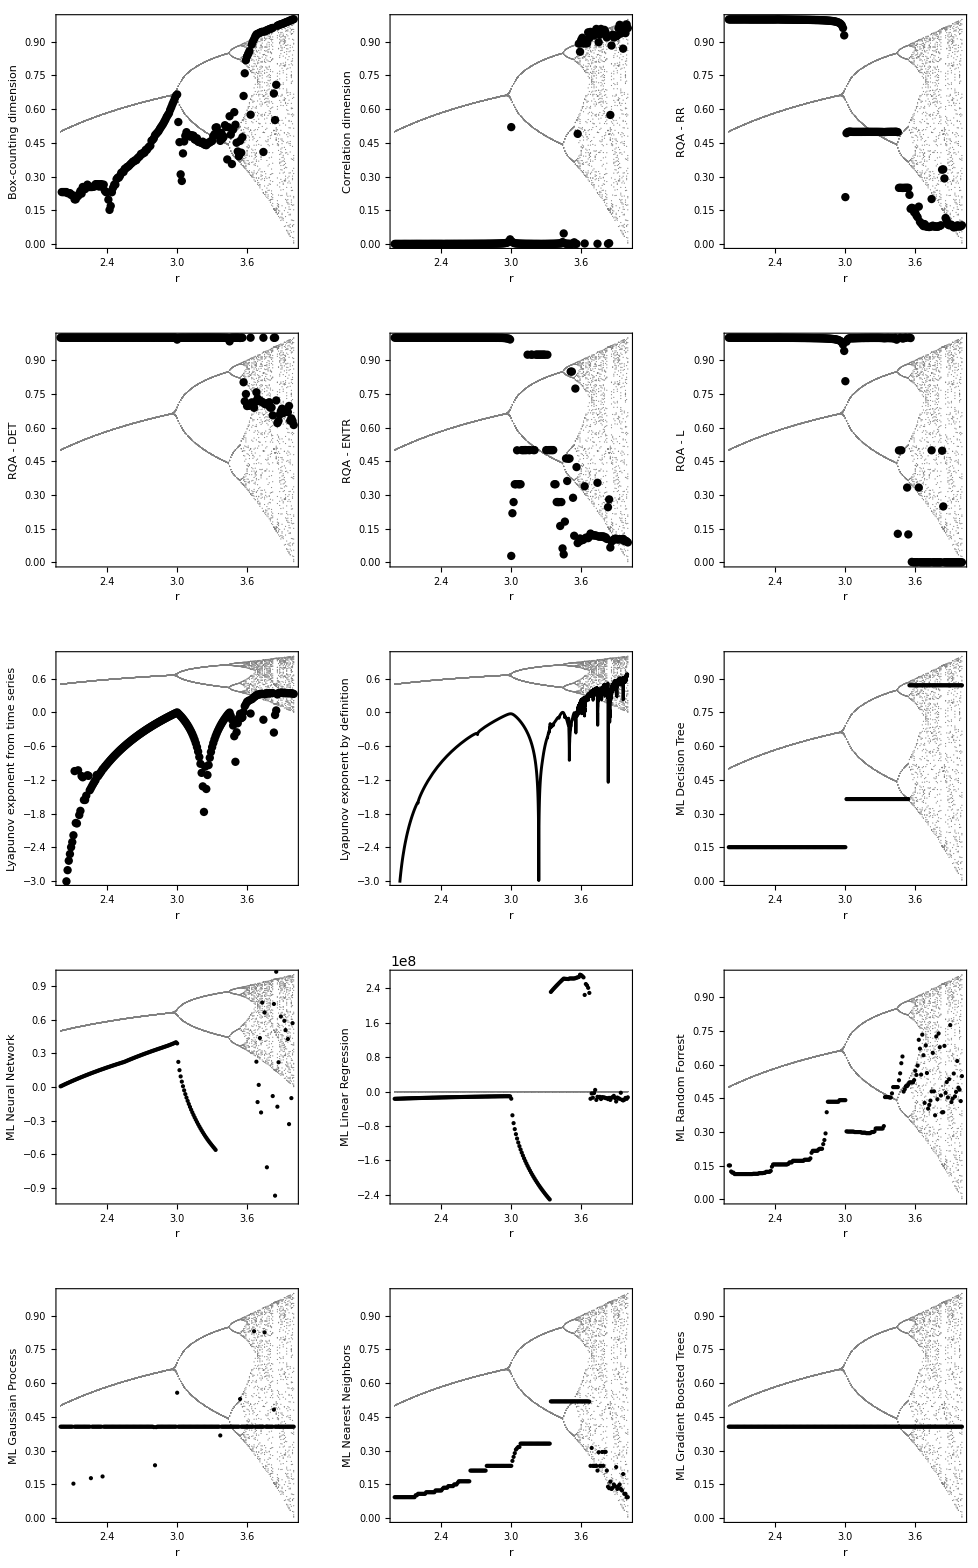

```mathematica
PPic4m=GraphicsGrid[{{pic111,pic222,pic444},{pic555,pic666,pic777},{pic333,picL,picm1},{picm2,picm3,picm4},{picm5,picm6,picm7}}] 
Export["PPic4m.png",PPic4m];
```